## Step-Wise Polymerization

Outline:

We have a (brute-force) function which reptates N m-monomer polymer chains w/o collisions

We’ll start with many non-colliding dimers and allow them to reptate

This is not super fast in the beginning.
Here’s a breakdown of the timing. Ideally we’d use temporal coherence using InsertionSort or similar

Number of Dimers  105

Bounding Box Collisions  0

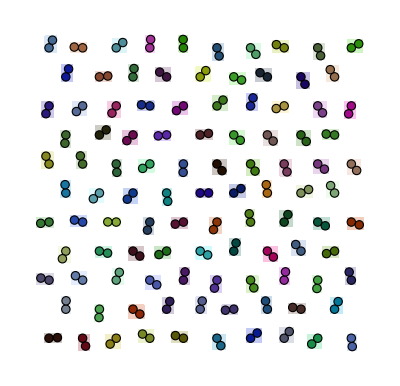

```mathematica
listOfPositions=hexagonalDimerConfiguration[40];
Echo[Length[listOfPositions],"Number of Dimers"];
bbs=axesAlignedBoundingBoxes/@listOfPositions;
cols=RandomColor[Length[bbs]];
Echo[connectivityMatrix[bbs]["ExplicitLength"],"Bounding Box Collisions"];
graphicMultiple=Graphics[MapThread[chainGraphic,{listOfPositions,bbs,cols}]]
```

```mathematica
Block[{
viscousDragging,
singleCollisionDetections,
multipleCollisionsDetection},

viscousDragging=First[RepeatedTiming[displacements[RandomInteger[{1,2}],#,0.1,0.1,RandomReal[2π]]&/@listOfPositions]];
singleCollisionDetections=First[RepeatedTiming[moveSingleChain[#,0.1]&/@listOfPositions]];
multipleCollisionsDetection=QuietEcho[First[RepeatedTiming[moveAllChains[listOfPositions,.1]]]];

Echo[viscousDragging,"Viscous Dragging Time"];
Echo[singleCollisionDetections,"Single Collision Detection Time"];
Echo[multipleCollisionsDetection,"Multiple Collisions Detection Time"];

]
```

Viscous Dragging Time  0.00733148

Single Collision Detection Time  0.00681805

Multiple Collisions Detection Time  0.019655

We keep track of the end particles

If any two collide, we merge the chains

we won’t concern ourselves with loops for now

Notes:

The reptation code makes use of `Nearest`, which is considerably slower for periodic boundary distances

We’ll deal with this later (?)

## Simulation

Dynamic

```mathematica
graphicMultiple=Graphics[chainGraphic/@listOfPositions];
Dynamic[graphicMultiple]
```

```mathematica
QuietEcho[
Do[
listOfPositions=moveAllChains[listOfPositions,.1];
graphicMultiple=Graphics[chainGraphic/@listOfPositions],
{10000}]
]
```

$Aborted

Frames

```mathematica
nestListWithMonitor[f_,init_,n_]:=Module[{it=0},PrintTemporary[ProgressIndicator[Dynamic[it/n]]];
NestList[(it++;f[#])&,init,n]]
```

```mathematica
positions=QuietEcho[nestListWithMonitor[moveAllChains[#,0.1]&,listOfPositions,5000]];
```

```mathematica
frames=Table[Graphics[chainGraphic/@positions[[i]],ImageSize->125],{i,1,5000,125}];
Manipulate[frames[[a]],{a,1,Length[frames],1}]
```

```mathematica
selectFrames=Table[Graphics[chainGraphic/@positions[[i]],ImageSize->125],{i,1,5000,125}];
Multicolumn[selectFrames,8,Appearance->"Horizontal",Frame->All]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Initialization Functions

### Correlated Polymers

```mathematica
collisionQ[nf_NearestFunction,bondLength_:1][candidatePt_]:=First[nf[candidatePt]]<bondLength

angularRange[correlation_]:={-1,1}(1-correlation)π

addCorrelatedParticleToChain[correlation_][chainSoFar_]:=Block[{
nf=Nearest[chainSoFar->"Distance"],
angleRange=angularRange[correlation],
lastAngle=ArcTan@@(chainSoFar[[-1]]-chainSoFar[[-2]]),
newAngle,candidate,collision
},

newAngle=RandomReal[angleRange]+lastAngle;
candidate=Last[chainSoFar]+AngleVector[newAngle];

collision=collisionQ[nf][candidate];
If[collision,chainSoFar,Append[chainSoFar,candidate]]

]

Clear[collisionFreeCorrelatedPolymerChain2D]
collisionFreeCorrelatedPolymerChain2D[numberUnits_,correlation_,origin_:{0,0},maxAttempts_:100]:=With[{start=Join[{origin},{AngleVector[origin,RandomReal[angularRange[correlation]]]}]},
NestWhile[addCorrelatedParticleToChain[correlation],start,Length[#]<numberUnits&,1,maxAttempts]
]

randomDimer[origin_]:=Join[{origin},{AngleVector[origin,RandomReal[2π]]}]
testDimerConfiguration[numberDimers_,size_]:=Table[randomDimer[RandomReal[{-size/2,size/2},2]],numberDimers]
initialDimerConfiguration[numberDimers_,size_]:=Block[{dimers=testDimerConfiguration[numberDimers,size],bbs,collisions},
bbs=axesAlignedBoundingBoxes/@dimers;
collisions=connectivityMatrix[bbs]["ExplicitLength"];
If[collisions>0,initialDimerConfiguration[numberDimers,size],dimers]
]

hexagonalDimerConfiguration[size_]:=Block[{hexagonalLatticeVectors={{1,0},{1/2,Sqrt[3]/2}},latticeCoords=Tuples[Range[-size,size,4],2],pts,dimers,bbs,collisions},
pts=Select[latticeCoords.hexagonalLatticeVectors,size/2>#[[1]]>-size/2&&size/2>#[[2]]>-size/2&];
randomDimer/@(pts+RandomReal[{-0.001,0.001},Dimensions[pts]])
]
```

### Viscous Dragging

```mathematica
precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]
```

```mathematica
displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
newPositions[index_] := newPositions[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex]},
newPositions[nextIndex] + Δ[[index]]
];
newPositions/@Range[Length[Δ]]
]
```

### Individual Chain Collision Detection

```mathematica
collisionFreeQ[positions_,nf_]:=Total[Length[nf[#,{All,1.-10^-6}]]&/@positions]<=Length[positions]

periodicDistanceFunction[size_][u_,v_]:=Norm@Mod[u-v,size,-size/2]

moveSingleChain[ positions_,ds_,size_:50,stickiness_:0.1]:= 
Block[{newPositions, newEnergy,nf},
newPositions= displacements[RandomInteger[{1,Length[positions]}],positions,ds,stickiness,RandomReal[2π]];
nf = Nearest[newPositions];
If[collisionFreeQ[newPositions,nf],newPositions,positions]
]
```

### Multiple Chains Collision Detection

```mathematica
axesAlignedBoundingBoxes[positions_]:={{-1/2,1/2},{-1/2,1/2}}+MinMax/@Transpose[positions]

pairWiseAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(xMaxA>xMinB&&xMinA<xMaxB)&&(yMaxA>yMinB&&yMinA<yMaxB)

horizontalAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(xMaxA>xMinB&&xMinA<xMaxB)

verticalAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(yMaxA>yMinB&&yMinA<yMaxB)

returnPointsInOverlap[{positionsA_,{{xMinA_,xMaxA_},{yMinA_,yMaxA_}}},{positionsB_,{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}}]:=With[
{
xMin=Max[xMinA,xMinB]-1/2,yMin=Max[yMinA,yMinB]-1/2,
xMax=Min[xMaxA,xMaxB]+1/2,yMax=Min[yMaxA,yMaxB]+1/2
},
Table[Select[pos,xMax>#[[1]]>xMin&&yMax>#[[2]]>yMin&],{pos,{positionsA,positionsB}}]
]

shortestDistanceLessThanOne[posA_,posB_]:=Block[{nf=Nearest[posA->"Distance"],i=1,d=2.,l=Length[posB]},
While[d>1. && i<=l,
d=First[nf[posB[[i]]]];
i++
];
d<1.
]

Clear[connectivityMatrixIndex,connectivityMatrixPair,connectivityMatrix]
connectivityMatrixIndex[bbs_,{i_,j_}]:=pairWiseAxesAlignedIntersection[bbs[[i]],bbs[[j]]]//Boole

connectivityMatrixPair[bbs_]:=Block[{s=Subsets[Range[Length[bbs]],{2}],l=Length[bbs],is},
SparseArray[s->(connectivityMatrixIndex[bbs,#]&/@s),{l,l}]
]

Clear[connectivityMatrixIndexHorizontal,connectivityMatrixIndexVertical]
connectivityMatrixIndexHorizontal[bbs_,{i_,j_}]:=horizontalAxesAlignedIntersection[bbs[[i]],bbs[[j]]]
connectivityMatrixIndexVertical[bbs_,{i_,j_}]:=verticalAxesAlignedIntersection[bbs[[i]],bbs[[j]]]//Boole

connectivityMatrix[bbs_]:=Block[{s=Subsets[Range[Length[bbs]],{2}],l=Length[bbs],pruneHorizontally},
pruneHorizontally=Select[s,connectivityMatrixIndexHorizontal[bbs,#]&];
SparseArray[pruneHorizontally->(connectivityMatrixIndexVertical[bbs,#]&/@pruneHorizontally),{l,l}]
]

pairwiseChainCollisionQ[{listOfPositions_,bbs_},{i_,j_}]:=Block[{
posA=listOfPositions[[i]],bbA=bbs[[i]],
posB=listOfPositions[[j]],bbB=bbs[[j]]
},

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];
If[Length[posA]==0||Length[posB]==0,False,shortestDistanceLessThanOne[posA,posB]]
]

compareEndPoints[listOfPositions_,{i_,j_}]:=
Block[{endsI=listOfPositions[[i,{1,-1}]],endsJ=listOfPositions[[j,{1,-1}]],vecs},
vecs=Tuples[{endsI,endsJ}];
Thread[SquaredEuclideanDistance@@@vecs<1]
]

mergeEndPoints[listOfPositions_,{i_,j_},pairwiseEndPointChecks_]:=With[{posI=listOfPositions[[i]],posJ=listOfPositions[[j]]},
Switch[pairwiseEndPointChecks,
{True,_,_,_},ReplacePart[listOfPositions,{{i},{j}}->Join[Reverse[posI],posJ]],
{False,True,_,_},ReplacePart[listOfPositions,{{i},{j}}->Join[posJ,posI]],
{False,False,True,_},ReplacePart[listOfPositions,{{i},{j}}->Join[posI,posJ]],
{False,False,False,True},ReplacePart[listOfPositions,{{i},{j}}->Join[posI,Reverse[posJ]]],
_,listOfPositions
]
]

chainCollisionsFreeQ[listOfPositions_]:=Block[{
listOfPos=listOfPositions,
bbs=axesAlignedBoundingBoxes/@listOfPositions,
mij,nonzero,collisions,collisionIndices,endpointChecks},

mij=connectivityMatrix[bbs];
If[mij["ExplicitLength"]==0,Echo["No Bounding Box Collisions"];Return[True]];

nonzero=mij["NonzeroPositions"];
collisions=pairwiseChainCollisionQ[{listOfPos,bbs},#]&/@nonzero;
If[Nor@@collisions,Echo["No Collisions"];True,Echo["Found Collisions!"];False]
]

checkForCollisions[{listOfPositions_,oldListOfPositions_}]:=Block[{
listOfPos=listOfPositions,
bbs=axesAlignedBoundingBoxes/@listOfPositions,
mij,nonzero,collisions,collisionIndices,endpointChecks},

mij=connectivityMatrix[bbs];
If[mij["ExplicitLength"]==0,Echo["No Bounding Box Collisions"];Return[listOfPos]];

nonzero=mij["NonzeroPositions"];
collisions=pairwiseChainCollisionQ[{listOfPos,bbs},#]&/@nonzero;
If[Nor@@collisions,Echo["No Collisions"];Return[listOfPos]];

collisionIndices= Extract[nonzero,Position[collisions,True]];
endpointChecks=compareEndPoints[listOfPos,#]&/@collisionIndices;
If[Nor@@Flatten[endpointChecks],Echo["No Mergers"];Return[oldListOfPositions]];

Do[
listOfPos=mergeEndPoints[listOfPos,collisionIndices[[a]],endpointChecks[[a]]],
{a,Length[collisionIndices]}
];

DeleteDuplicates[listOfPos]

]

moveAllChains[listOfPositions_,ds_]:= Block[{listOfPos=listOfPositions},
listOfPos=moveSingleChain[#,ds]&/@listOfPos;
checkForCollisions[{listOfPos,listOfPositions}]
]
```

### Visualization

```mathematica
chainGraphic[positions_,bb_,col_:RandomColor[]]:= {
{Opacity[0.25],col,Rectangle@@Transpose[bb]},
{FaceForm[None],EdgeForm[col//Darker],Disk[#,1/2]&/@positions[[2;;-2]]},
{FaceForm[col//Darker],EdgeForm[Black],Disk[#,1/2]&/@positions[[{1,-1}]]}
}

chainGraphic[positions_]:= {
{FaceForm[None],EdgeForm[Black],Disk[#,1/2]&/@positions[[2;;-2]]},
{FaceForm[LightGray],EdgeForm[Black],Disk[#,1/2]&/@positions[[{1,-1}]]}
}
```